```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ManPaths=Function[{idx,style},Graphics[Prepend[Line/@ReadList["data/"<>ToString[idx]<>".list"]⟦All,1,1;;-1;;10⟧,style]]];
RaptorPaths=Function[{idx,style},Graphics[Prepend[Line/@ReadList["data/"<>ToString[idx]<>".list"]⟦All,2,1;;-1;;10⟧,style]]];
```

```mathematica
ParallelMap[Export["frames/"<>IntegerString[#,10,3]<>".gif",Show[ListPlot[{0,0},PlotRange->{{-50,50},{-50,50}},AspectRatio->1,ImageSize->800,Frame->True,Axes->False],ManPaths[#,Blue],RaptorPaths[#,Red]]];&,Range[0,10]];
```

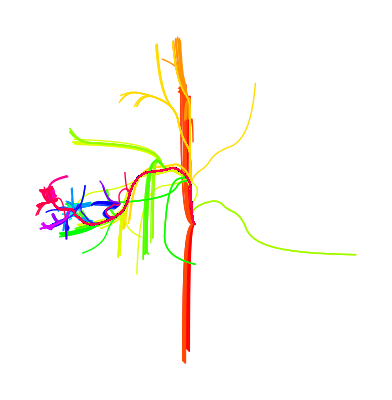

```mathematica
start=0;
stop =20;
Show@@ParallelMap[ManPaths[#,Hue[#/(stop-start+1)]]&,Range[start,stop]]
```